```mathematica
(* t99 we take to be the time such that P(T_total < t99) = 0.99 and similar for t95. Here we solve for t99 and t95*)
```

# Some Definitions

```mathematica
Λ[n_]:=DiagonalMatrix[Table[-i*(i-1)/2,{i,n,2,-1}]] +DiagonalMatrix[Table[i*(i-1)/2, {i,n,3,-1}],1];
```

```mathematica
Λ[5] //MatrixForm
```

(-10 | 10 | 0 | 0
0 | -6 | 6 | 0
0 | 0 | -3 | 3
0 | 0 | 0 | -1)

```mathematica
α[n_]:=Table[If[i==1,1,0],{i,1,n-1}];
```

```mathematica
α[5]
```

{1,0,0,0}

```mathematica
One[n_]:=Table[1,{i,1,n-1}];
```

```mathematica
One[5]
```

{1,1,1,1}

# Calculation

```mathematica
t99[n_] := NSolve[1-α[n].MatrixExp[t*Λ[n]].One[n]==0.99,t, PositiveReals]
```

```mathematica
t95[n_]:=NSolve[1-α[n].MatrixExp[t*Λ[n]].One[n]==0.95,t,PositiveReals]
```

```mathematica
t999[n_]:= NSolve[1-α[n].MatrixExp[t*Λ[n]].One[n]==0.999,t,PositiveReals]
```

```mathematica
t50[n_]:=NSolve[1-α[n].MatrixExp[t*Λ[n]].One[n]==0.5,t,PositiveReals]
```

```mathematica
Times99 = ParallelTable[t99[n], {n,5,100,5}];
```

$Aborted

```mathematica
Times95 = ParallelTable[t95[n], {n,5,100,5}];
```

```mathematica
Times50 =ParallelTable[t50[n], {n,5,100,5}];
```

```mathematica
Times999=ParallelTable[t999[n],{n,5,100,5}]
```

{{{t→7.6009}},{{t→7.8057}},{{t→7.87284}},{{t→7.90628}},{{t→7.92632}},{{t→7.93968}},{{t→7.94921}},{{t→7.95636}},{{t→7.96192}},{{t→7.96636}},{{t→7.97}},{{t→7.97303}},{{t→7.9756}},{{t→7.97779}},{{t→7.9797}},{{t→7.98137}},{{t→7.98284}},{{t→7.98414}},{{t→7.98531}},{{t→7.98637}}}

# Plotting

```mathematica
Times99 = Flatten[t /. Times99];
Times95 = Flatten[t /. Times95];
```

ReplaceAll::reps: {5.2983,5.50309,5.57023,5.60368,5.62372,5.63707,5.64661,5.65375,5.65931,5.66376,«10»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {3.68843,3.89321,3.96035,3.9938,4.01384,4.02719,4.03672,4.04387,4.04943,4.05388,«10»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

```mathematica
Times50 = Flatten[t /. Times50];
```

ReplaceAll::reps: {1.336,1.53896,1.60593,1.63934,1.65937,1.67271,1.68224,1.68939,1.69494,1.69939,«10»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

```mathematica
data99 = Table[{5*i,Times99[[i]]}, {i,1,20}];
data95 = Table[{5*i,Times95[[i]]}, {i,1,20}];
```

```mathematica
data50 = Table[{5*i,Times50[[i]]}, {i,1,20}];
```

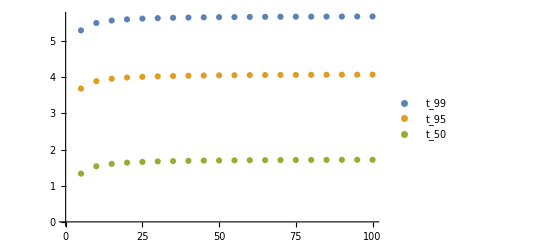

```mathematica
ListPlot[{data99,data95,data50},PlotLegends->{"t_99","t_95","t_50"},PlotRange->Automatic]
```